```mathematica
(* The paper uses the color scheme BlueGreenYellow for the density images. *)
(* TODO: Gravity shifted absorption image *)
```

## Thermal calculations.

#### assuming running up to the dressed - state illustrations in the bubble*.nb

```mathematica
Δ1=cDelta;
Ωc = cOmega;
geff =-.00000001;
```

#### interfacing Nathan’s code with my toy model

```mathematica
AdiabaticEnergiesChipC2[Delta_,Omega_,x_,y_,z_]:=(adiabaticEnergiesTOY[Delta,Omega,x,y,z][[1]]);
XCosineAccurateC2[x_,y_,z_]:=1;
ClearAll[MagFracC2];
MagFracC2[x_,y_,z_]:=1;
x1=0.;
y1=0.;
z1=0.;
```

#### quick and dirty finding minimum energy of the bubble potential so that we can subtract it. this is slightly dodgy since I' m just looking along the x, y, and z axes.

Approx. min [Hz] = 17000.

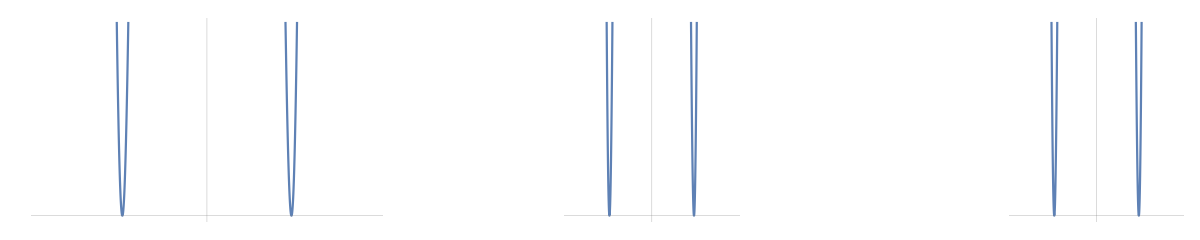

```mathematica
testf[x_,y_,z_]:=(*-geff mRb 9.81 (z-z1)/h+*)AdiabaticEnergiesChipC2[Δ1, Ωc  XCosineAccurateC2[x,y,z]MagFracC2[x,y,z ]    ,x,y,z];

t= Table[{z,testf[x1,y1,z]},{z,z1-.3 mm,z1+.3mm,0.2*^-6}];
(*ListPlot[%,AxesLabel->{"z","E"}]*)
t2= Table[{x,testf[x,y1,z1]},{x,-.3 mm,+.3mm,0.2*^-6}];
(*ListPlot[%,AxesLabel->{"x","E"}]*)
t3= Table[{y,testf[x1,y,z1]},{y,-.3 mm,+.3mm,0.2*^-6}];
(*ListPlot[%,AxesLabel->{"y","E"}]*)
minloc= Position[t[[All,2]],Min[t[[All,2]]]][[1,1]];
minloc2= Position[t2[[All,2]],Min[t2[[All,2]]]][[1,1]];
minloc3= Position[t3[[All,2]],Min[t3[[All,2]]]][[1,1]];
zmin = t[[Position[t[[All,2]],Min[t[[All,2]]]][[1,1]],1]];
xmin = t2[[Position[t2[[All,2]],Min[t2[[All,2]]]][[1,1]],1]];
ymin = t3[[Position[t3[[All,2]],Min[t3[[All,2]]]][[1,1]],1]];
ShiftVal=(*-geff mRb 9.81 (zmin-z1)/h+*)AdiabaticEnergiesChipC2[Δ1,Ωc  XCosineAccurateC2[x1,y1,zmin]MagFracC2[x1,y1,zmin ],x1,y1,zmin];
ShiftVal2=AdiabaticEnergiesChipC2[Δ1,Ωc  XCosineAccurateC2[xmin,y1,z1]MagFracC2[xmin,y1,z1 ],xmin,y1,z1];
ShiftVal3=AdiabaticEnergiesChipC2[Δ1,Ωc  XCosineAccurateC2[x1,ymin,z1]MagFracC2[x1,ymin,z1 ],x1,ymin,z1];
BestShiftVal = Min[{ShiftVal,ShiftVal2,ShiftVal3}];
Print["Approx. min [Hz] = "<>ToString@BestShiftVal];

(*potS[x_,y_,z_]=(-BestShiftVal(*-geff mRb 9.81 (z-z1)/h*)+AdiabaticEnergiesChipC2[Δ1, Ωc XCosineAccurateC2[x ,y ,z ] MagFracC2[x ,y ,z ],x,y,z ]);*)
(*potS[x_,y_,z_]=(-BestShiftVal(*-geff mRb 9.81 (z-z1)/h*)+AdiabaticEnergiesChipC2[Δ1, Ωc XCosineAccurateC2[x ,y ,z ] ,x,y,z ]);*)
ClearAll[potS,x,y,z]
potS[x_,y_,z_]:=(-BestShiftVal(*-geff mRb 9.81 (z-z1)/h*)+AdiabaticEnergiesChipC2[Δ1, Ωc* XCosineAccurateC2[x ,y ,z ] *MagFracC2[x ,y ,z ],x,y,z] );

aBox =300 μm;  (* 300 um for ZHB, 600 um for ZZH, but make sure to adjust BoltzPixel accordingly (4.04 um and 3 times that, respectively)! *)

Block[{plotMax=40*20,plotMin=-10},
GraphicsGrid[{{
Plot[potS[x mm,y1,z1],{x ,(x1-aBox)/mm,(x1+aBox)/mm},Axes->False,AspectRatio->1/2,ImageSize->500,GridLines->{{x1/mm},{0}},PlotRange->{plotMin,plotMax}],
Plot[potS[x1,y mm,z1],{y ,(y1-aBox(*/2*))/mm,(y1+aBox(*/2*))/mm},Axes->False,AspectRatio->1,ImageSize->250,GridLines->{{y1/mm},{0}},PlotRange->{plotMin,plotMax}],
Plot[potS[x1,y1,z mm],{z,(z1-aBox(*/2*))/mm,(z1+aBox(*/2*))/mm},AspectRatio->1,ImageSize->250,GridLines->{{z1/mm},{0}},Axes->False,PlotRange->{plotMin,plotMax}]
}}]
]
```

```mathematica
HarmonicEntropy[T_] = 3/2+(3 Log[T])/2+Log[(2 √2 π^(3/2) ((kb T)/M)^(3/2))/(√(ωx^2 ωy^2 ωz^2))];
Λ[T_] := Sqrt[2 π ℏ^2/(m kB T)] /. {kB->1.3806*^-23,m->1.443*^-25,ℏ->1.0546*^-34};
HarmonicEntropy[450*^-9] /. {kb ->1.3806488*^-23,M->1.443*^-25,ωx->2 π 31.46,ωy->2 π 98.43,ωz->2 π 100.8}
HarmonicEntropy[90*^-9] /. {kb ->1.3806488*^-23,M->1.44*^-25,ωx->2 π 31.46,ωy->2 π 98.43,ωz->2 π 100.8}
HarmonicEntropy[90*^-9] /. {kb ->1.3806488*^-23,M->1.44*^-25,ωx->2 π 25,ωy->2 π 40,ωz->2 π 40}
```

-50.9086

-55.7338

-53.6792

```mathematica
BoltzPixel= 4.04μm;
```

```mathematica
Parallelize[BoltzTable=Table[Exp[-potS[x mm,y mm,z mm]/kT],
{x,x1/mm-aBox/mm,x1/mm+aBox/mm,BoltzPixel/mm},{y,y1/mm-aBox/mm(*/2*),y1/mm+aBox/mm(*/2*),BoltzPixel/mm},{z,z1/mm-aBox/mm(*/2*),z1/mm+aBox/mm(*/2*),BoltzPixel/mm}];] (* x is long axis *)
BoltzTable //Dimensions
```

{149,149,149}

```mathematica
nKPerHz
```

0.0479924

```mathematica
Cloud850= BoltzTable /. kT->(*320*)(temperature*10^9)/nKPerHz;
```

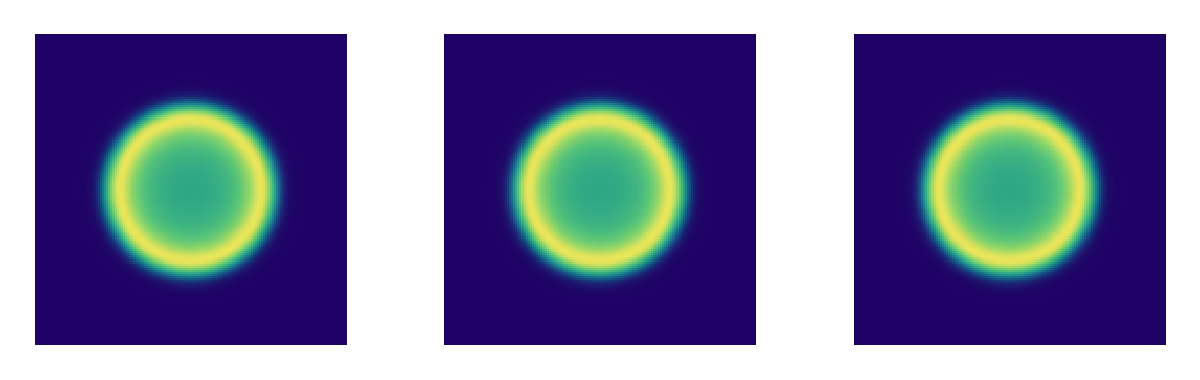

```mathematica
defaultArrayPlotOptions=Options@ArrayPlot;
SetOptions[ArrayPlot,{ColorFunction->"BlueGreenYellow"}];
BlurValue =2; (* in BoltzPixels *) 
GraphicsGrid[{{
ArrayPlot[Reverse[GaussianFilter[Transpose[Total[Cloud850,{2}]],BlurValue],2] ,PlotRange->All(*,AspectRatio->2*)(*,ColorFunction->"Thermometer"*),FrameTicks->Automatic,ImageSize->400,FrameLabel->{"x","z"}],
ArrayPlot[Reverse[GaussianFilter[Transpose[Total[Cloud850,{1}]],BlurValue],2] ,PlotRange->All(*,AspectRatio->2*)(*,ColorFunction->"Thermometer"*),FrameTicks->Automatic,ImageSize->400,FrameLabel->{"x","y"}],
ArrayPlot[Reverse[GaussianFilter[Transpose[Total[Cloud850,{3}]],BlurValue],2] ,PlotRange->All,AspectRatio->1(*,ColorFunction->"Thermometer"*),FrameTicks->Automatic,ImageSize->400,FrameLabel->{"y","z"}]}}]

SetOptions[ArrayPlot,defaultArrayPlotOptions];
```

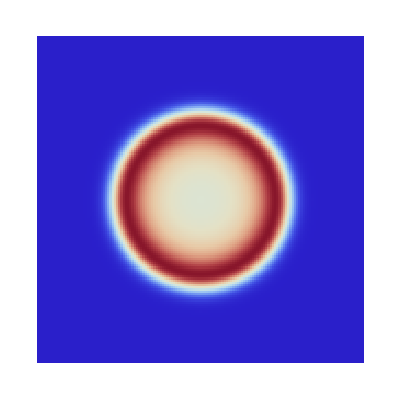

```mathematica
absorptionImage=(*Legended[*)
ArrayPlot[(*Reverse[GaussianFilter[*)Transpose[Total[Cloud850,{3}]](*,BlurValue],2]*) ,PlotRange->All(*,AspectRatio->2*),ColorFunction->"ThermometerColors"(*,FrameTicks->Automatic*)(*,ImageSize->400*)(*,FrameLabel->{"y","x"}*)](*FUDGED!*)(*,
BarLegend["BlueGreenYellow",Ticks->None,LegendLabel->"Population"]
]*)
```

```mathematica
ArrayPlot[(*Reverse[GaussianFilter[*)Transpose[Total[Cloud850,{3}]](*,BlurValue],2]*) ,PlotRange->All(*,AspectRatio->2*),ColorFunction->"ThermometerColors"(*,FrameTicks->Automatic*)(*,ImageSize->400*)(*,FrameLabel->{"y","x"}*)](*FUDGED!*)(*,
BarLegend["BlueGreenYellow",Ticks->None,LegendLabel->"Population"]
]*)
```

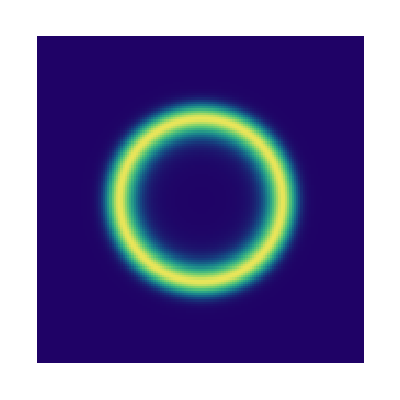

```mathematica
crossSectionImage=(*Legended[*)
ArrayPlot[Transpose@Cloud850[[;;,;;,75]] ,PlotRange->All(*,AspectRatio->2*),ColorFunction->"BlueGreenYellow",(*FrameTicks->Automatic,*)(*ImageSize->400,*)FrameLabel->{"y","x"},(*FUDGED!*)
FrameTicks->None,
Ticks->None](*,
BarLegend["BlueGreenYellow",Ticks->None,LegendLabel->"Population"]
]*)
```

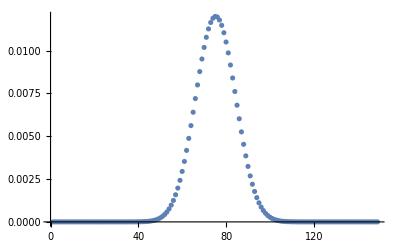

```mathematica
ListPlot[Cloud850[[40,40,;;]]]
```

## Now with gravity

```mathematica
AdiabaticEnergiesChipC2[Delta_,Omega_,x_,y_,z_]:=(adiabaticEnergiesTOY[Delta,Omega,x,y,z][[1]])+gravPotential[x,0.1];
XCosineAccurateC2[x_,y_,z_]:=1;
ClearAll[MagFracC2];
MagFracC2[x_,y_,z_]:=1;
x1=0.;
y1=0.;
z1=0.;
```

#### quick and dirty finding minimum energy of the bubble potential so that we can subtract it. this is slightly dodgy since I' m just looking along the x, y, and z axes.

Approx. min [Hz] = -16407.7

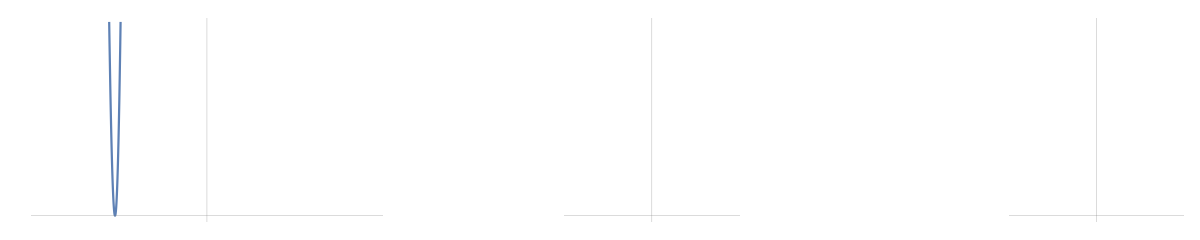

```mathematica
testf[x_,y_,z_]:=(*-geff mRb 9.81 (z-z1)/h+*)AdiabaticEnergiesChipC2[Δ1, Ωc  XCosineAccurateC2[x,y,z]MagFracC2[x,y,z ]    ,x,y,z];

t= Table[{z,testf[x1,y1,z]},{z,z1-.3 mm,z1+.3mm,0.2*^-6}];
(*ListPlot[%,AxesLabel->{"z","E"}]*)
t2= Table[{x,testf[x,y1,z1]},{x,-.3 mm,+.3mm,0.2*^-6}];
(*ListPlot[%,AxesLabel->{"x","E"}]*)
t3= Table[{y,testf[x1,y,z1]},{y,-.3 mm,+.3mm,0.2*^-6}];
(*ListPlot[%,AxesLabel->{"y","E"}]*)
minloc= Position[t[[All,2]],Min[t[[All,2]]]][[1,1]];
minloc2= Position[t2[[All,2]],Min[t2[[All,2]]]][[1,1]];
minloc3= Position[t3[[All,2]],Min[t3[[All,2]]]][[1,1]];
zmin = t[[Position[t[[All,2]],Min[t[[All,2]]]][[1,1]],1]];
xmin = t2[[Position[t2[[All,2]],Min[t2[[All,2]]]][[1,1]],1]];
ymin = t3[[Position[t3[[All,2]],Min[t3[[All,2]]]][[1,1]],1]];
ShiftVal=(*-geff mRb 9.81 (zmin-z1)/h+*)AdiabaticEnergiesChipC2[Δ1,Ωc  XCosineAccurateC2[x1,y1,zmin]MagFracC2[x1,y1,zmin ],x1,y1,zmin];
ShiftVal2=AdiabaticEnergiesChipC2[Δ1,Ωc  XCosineAccurateC2[xmin,y1,z1]MagFracC2[xmin,y1,z1 ],xmin,y1,z1];
ShiftVal3=AdiabaticEnergiesChipC2[Δ1,Ωc  XCosineAccurateC2[x1,ymin,z1]MagFracC2[x1,ymin,z1 ],x1,ymin,z1];
BestShiftVal = Min[{ShiftVal,ShiftVal2,ShiftVal3}];
Print["Approx. min [Hz] = "<>ToString@BestShiftVal];

(*potS[x_,y_,z_]=(-BestShiftVal(*-geff mRb 9.81 (z-z1)/h*)+AdiabaticEnergiesChipC2[Δ1, Ωc XCosineAccurateC2[x ,y ,z ] MagFracC2[x ,y ,z ],x,y,z ]);*)
(*potS[x_,y_,z_]=(-BestShiftVal(*-geff mRb 9.81 (z-z1)/h*)+AdiabaticEnergiesChipC2[Δ1, Ωc XCosineAccurateC2[x ,y ,z ] ,x,y,z ]);*)
ClearAll[potS,x,y,z]
potS[x_,y_,z_]:=(-BestShiftVal(*-geff mRb 9.81 (z-z1)/h*)+AdiabaticEnergiesChipC2[Δ1, Ωc* XCosineAccurateC2[x ,y ,z ] *MagFracC2[x ,y ,z ],x,y,z] );

aBox =300 μm;  (* 300 um for ZHB, 600 um for ZZH, but make sure to adjust BoltzPixel accordingly (4.04 um and 3 times that, respectively)! *)

Block[{plotMax=40*20,plotMin=-10},
GraphicsGrid[{{
Plot[potS[x mm,y1,z1],{x ,(x1-aBox)/mm,(x1+aBox)/mm},Axes->False,AspectRatio->1/2,ImageSize->500,GridLines->{{x1/mm},{0}},PlotRange->{plotMin,plotMax}],
Plot[potS[x1,y mm,z1],{y ,(y1-aBox(*/2*))/mm,(y1+aBox(*/2*))/mm},Axes->False,AspectRatio->1,ImageSize->250,GridLines->{{y1/mm},{0}},PlotRange->{plotMin,plotMax}],
Plot[potS[x1,y1,z mm],{z,(z1-aBox(*/2*))/mm,(z1+aBox(*/2*))/mm},AspectRatio->1,ImageSize->250,GridLines->{{z1/mm},{0}},Axes->False,PlotRange->{plotMin,plotMax}]
}}]
]
```

```mathematica
(*HarmonicEntropy[T_] = 3/2+(3 Log[T])/2+Log[(2 √2 π^(3/2) ((kb T)/M)^(3/2))/(√(ωx^2 ωy^2 ωz^2))];
Λ[T_] := Sqrt[2 π ℏ^2/(m kB T)] /. {kB->1.3806*^-23,m->1.443*^-25,ℏ->1.0546*^-34};
HarmonicEntropy[450*^-9] /. {kb ->1.3806488*^-23,M->1.443*^-25,ωx->2 π 31.46,ωy->2 π 98.43,ωz->2 π 100.8}
HarmonicEntropy[90*^-9] /. {kb ->1.3806488*^-23,M->1.44*^-25,ωx->2 π 31.46,ωy->2 π 98.43,ωz->2 π 100.8}
HarmonicEntropy[90*^-9] /. {kb ->1.3806488*^-23,M->1.44*^-25,ωx->2 π 25,ωy->2 π 40,ωz->2 π 40}*)
```

```mathematica
BoltzPixel= 4.04μm;
```

```mathematica
Parallelize[BoltzTableG=Table[Exp[-potS[x mm,y mm,z mm]/kT],
{x,x1/mm-aBox/mm,x1/mm+aBox/mm,BoltzPixel/mm},{y,y1/mm-aBox/mm(*/2*),y1/mm+aBox/mm(*/2*),BoltzPixel/mm},{z,z1/mm-aBox/mm(*/2*),z1/mm+aBox/mm(*/2*),BoltzPixel/mm}];] (* x is long axis *)
BoltzTable //Dimensions
```

{149,149,149}

```mathematica
nKPerHz
```

0.0479924

```mathematica
Cloud850G= BoltzTableG /. kT->320/nKPerHz;
```

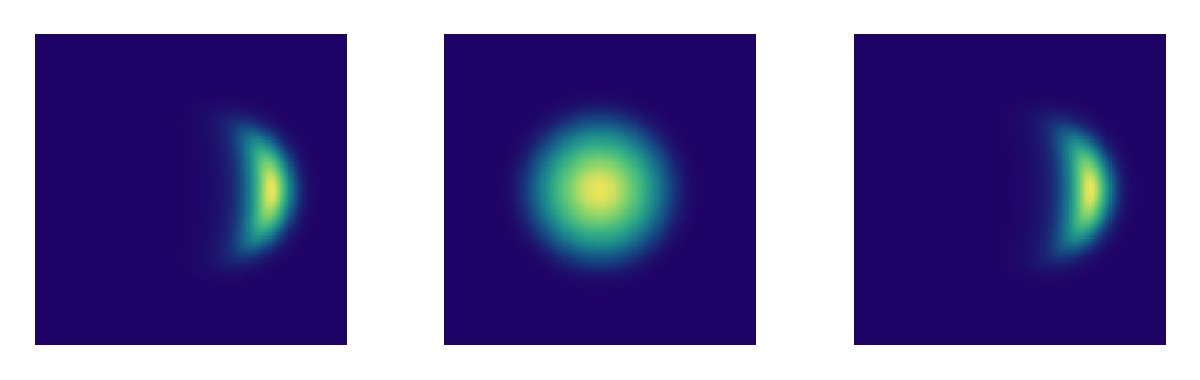

```mathematica
defaultArrayPlotOptions=Options@ArrayPlot;
SetOptions[ArrayPlot,{ColorFunction->"BlueGreenYellow"}];
BlurValue =2; (* in BoltzPixels *) 
GraphicsGrid[{{
ArrayPlot[Reverse[GaussianFilter[Transpose[Total[Cloud850G,{2}]],BlurValue],2] ,PlotRange->All(*,AspectRatio->2*)(*,ColorFunction->"Thermometer"*),FrameTicks->Automatic,ImageSize->400,FrameLabel->{"x","z"}],
ArrayPlot[Reverse[GaussianFilter[Transpose[Total[Cloud850G,{1}]],BlurValue],2] ,PlotRange->All(*,AspectRatio->2*)(*,ColorFunction->"Thermometer"*),FrameTicks->Automatic,ImageSize->400,FrameLabel->{"x","y"}],
ArrayPlot[Reverse[GaussianFilter[Transpose[Total[Cloud850G,{3}]],BlurValue],2] ,PlotRange->All,AspectRatio->1(*,ColorFunction->"Thermometer"*),FrameTicks->Automatic,ImageSize->400,FrameLabel->{"y","z"}]}}]

SetOptions[ArrayPlot,defaultArrayPlotOptions];
```

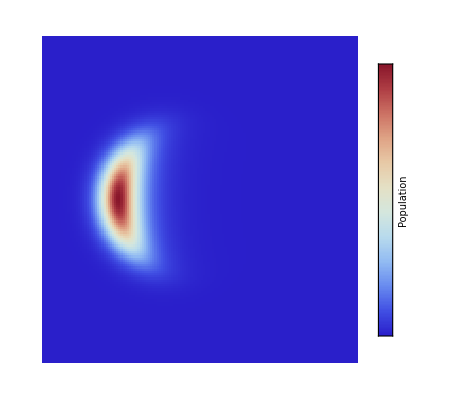

```mathematica
absorptionImageGrav=Legended[
ArrayPlot[(*Transpose@*)(*Reverse[*)(*GaussianFilter[Transpose[*)Transpose@Total[Cloud850G,{3}](*],BlurValue]*)(*,2]*) ,
PlotRange->All(*,AspectRatio->2*),
ColorFunction->"ThermometerColors"(*,FrameTicks->Automatic*),(*ImageSize->400,*)(*FrameLabel->{"y","x"},*)
DataReversed->True],

BarLegend["ThermometerColors",Ticks->None,LegendLabel->"Population"]
]
```

```mathematica
cnvtCoor[x_,xmin_]:=(x-xmin)/(BoltzPixel*10^6);
cnvtc[x_]:=cnvtCoor[x,xMin];
```

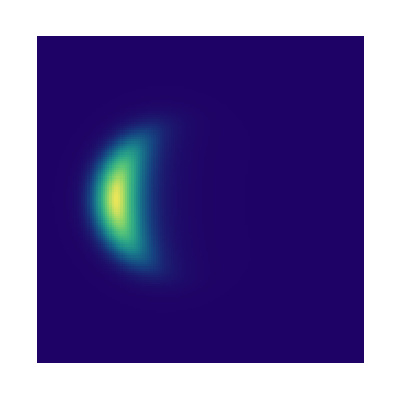

```mathematica
arrayFrameTicks={
{{{cnvtc[-yPotMin],"-y_min"},{cnvtc@0,0},{cnvtc@yPotMin,"y_min"}},None},
{{{cnvtc[-xPotMin],"-x_min"},{cnvtc@0,0},{cnvtc@xPotMin,"x_min"}},None}
};

arrayFrameTicks={
{None,None},
{{{cnvtc[-xPotMin],"-x_min"},{cnvtc@0,0},{cnvtc@xPotMin,"x_min"}},None}
};

absorptionImageGravLgndls=ArrayPlot[Transpose@Total[Cloud850G,{3}] ,
PlotRange->All,
ColorFunction->"BlueGreenYellow"(*,
FrameLabel->{"y","x"}*),
DataReversed->True,
FrameTicks->arrayFrameTicks]
```

```mathematica
cnvtc[yPotMin]/10^6
```

0.000111386

## Putting it all together

```mathematica
atomGrid=Grid@{{
Show[crossSectionImage,PlotLabel->"Population cross-section"],
Show[absorptionImage,PlotLabel->"Population, integrate z axis"],Show[absorptionImageGrav,PlotLabel->"Population, w/ 5% gravity",
Background->LightGray]
}}
```